```mathematica
study42 = z/.{ToRules[NRoots[Sum[z^x Binomial[1456,x]*Binomial[2895,(68-x)],{x,0,68}],z]]}
```

{-3.35687,-3.25556,-3.1744,-3.10398,-3.04065,-2.98251,-2.92841,-2.87759,-2.8295,-2.78374,-2.74002,-2.69807,-2.65772,-2.61878,-2.58114,-2.54467,-2.50927,-2.47487,-2.44138,-2.40873,-2.37688,-2.34576,-2.31533,-2.28555,-2.25638,-2.22778,-2.19972,-2.17217,-2.14511,-2.11849,-2.09231,-2.06654,-2.04115,-2.01614,-1.99146,-1.96712,-1.94309,-1.91935,-1.89589,-1.87269,-1.84974,-1.82702,-1.80451,-1.7822,-1.76008,-1.73812,-1.71632,-1.69465,-1.6731,-1.65165,-1.63029,-1.60898,-1.58772,-1.56646,-1.5452,-1.52389,-1.5025,-1.48098,-1.4593,-1.43737,-1.41513,-1.39248,-1.36926,-1.3453,-1.32027,-1.29369,-1.26456,-1.23027}

```mathematica
study41 = z/.{ToRules[NRoots[Sum[z^x Binomial[2635,x]*Binomial[2634,(24-x)],{x,0,24}],z]]}
```

{-1.26469,-1.22776,-1.19768,-1.17118,-1.14699,-1.12446,-1.10319,-1.08291,-1.06342,-1.04459,-1.02629,-1.00842,-0.990897,-0.973644,-0.956585,-0.939643,-0.922737,-0.905774,-0.88864,-0.871185,-0.853192,-0.83431,-0.813869,-0.790103}

```mathematica
NRoots[Sum[z^x Binomial[2635,x]*Binomial[2634,(24-x)],{x,0,24}],z]
```

z==-1.26469||z==-1.22776||z==-1.19768||z==-1.17118||z==-1.14699||z==-1.12446||z==-1.10319||z==-1.08291||z==-1.06342||z==-1.04459||z==-1.02629||z==-1.00842||z==-0.990897||z==-0.973644||z==-0.956585||z==-0.939643||z==-0.922737||z==-0.905774||z==-0.88864||z==-0.871185||z==-0.853192||z==-0.83431||z==-0.813869||z==-0.790103

```mathematica
lamall=z/.{ToRules[NRoots[Sum[z^x Binomial[1456,x]*Binomial[2895,(68-x)],{x,0,68}], z]]};
Plus@@(1/(1-lamall/1.5))
```

29.1305

```mathematica
Plus@@(1/(1-lamall/1.0))
```

22.7552

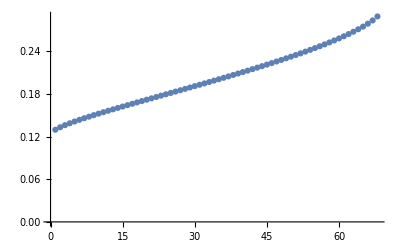

```mathematica
ListPlot[1/(1-lamall/0.5)]
```